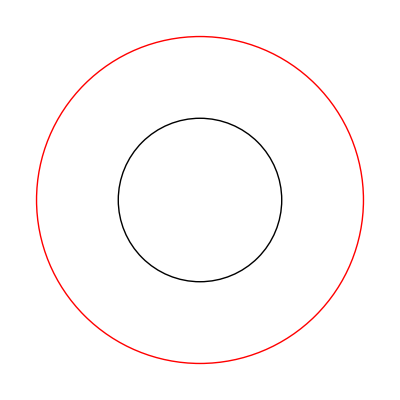

```mathematica
Graphics[{{Red,Circle[]},{Black,Circle[{0,0},{.5,.5}]}}]
```

```mathematica
circles={};
colors={Red,Green,Blue};
```

```mathematica
For[i=0,i<4,i++,

circles=Append[circles,{colors[[Mod[i,3]+1]],Circle[]}]
]
```

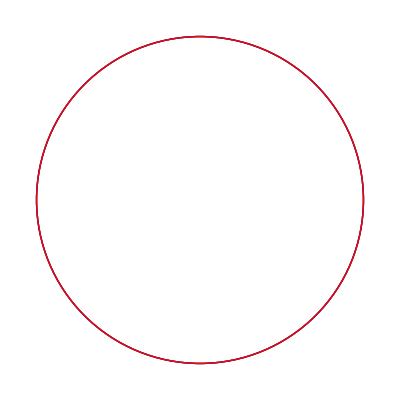

```mathematica
Graphics[circles]
```